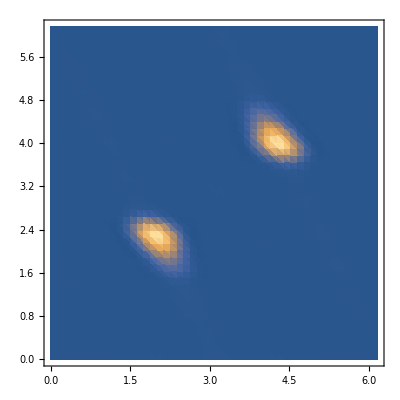

```mathematica
fat="/home/leonard/Documents/Projects/PhysicalDistance/Codes/data/KickedRotorID/";
prefix="k_5.0m_30/";
ind=Import[fat<>prefix<>"inds.dat","Table"];
pos=Import[fat<>prefix<>"pos.dat","Table"];
ListDensityPlot[Flatten/@Transpose[{pos,ind}],{PlotRange->All}]
```

```mathematica
dmat=Import[fat<>prefix<>"DMat.dat","Table"]//Flatten;
Histogram[Flatten[dmat]];
```

```mathematica
res=Table[fat="/home/leonard/Documents/Projects/PhysicalDistance/Codes/data/KickedRotorID/";
prefix="k_1.5m_"<>ToString[m]<>"/";
dmat=Import[fat<>prefix<>"DMat.dat","Table"]//Flatten;
(*Histogram[Flatten[dmat]];*)
{m,Variance[dmat],Mean[dmat]
},{m,{10,14,18,20,24,28,30}}];
```

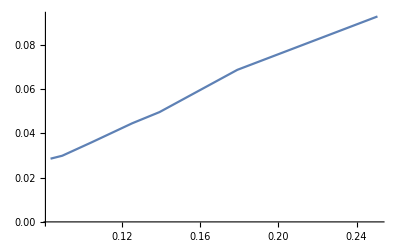

```mathematica
ListLinePlot[{(√(2.*π))/(#[[1]]),#[[3]]}&/@res]
```

```mathematica
LinearModelFit[{(√(2.*π))/(#[[1]]),#[[2]]}&/@res,x,x]
```

FittedModel[-0.000810254+0.0195269 x]

```mathematica
%135["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.000810254 | 0.0000672965 | -12.0401 | 0.0000697566
x | 0.0195269 | 0.000450949 | 43.3018 | 1.23963×10^-7